```mathematica
f[x_]:=ReplaceList[Range[x],{___,a_,___,b_,___}/;(IntegerQ[-1/2 (1-√(1+8 (a b)))])==True->a.b]
```

```mathematica
Table[f[n]//Length,{n,0,200}]
```

{0,0,0,2,2,4,5,7,7,9,10,12,14,16,17,22,22,24,25,27,29,34,35,37,39,41,42,44,45,47,52,54,54,59,60,64,65,67,68,73,74,76,81,83,85,90,91,93,95,97,98,103,105,107,108,113,115,120,121,123,127,129,130,134,134,139,143,145,146,151,155,157,159,161,162,167,169,174,178,180,182,184,185,187,192,197,198,203,204,206,210,215,216,221,222,227,229,231,232,236,237,239,244,246,248,259,260,262,264,266,270,275,276,278,283,288,290,295,296,301,306,308,309,314,315,317,320,322,322,327,331,333,338,342,343,348,349,351,355,357,362,367,368,372,373,378,379,384,386,388,392,394,396,401,405,410,415,417,418,423,424,428,429,431,432,443,444,446,450,452,457,462,464,466,471,476,477,482,483,485,490,492,496,501,503,508,513,518,519,524,527,529,531,533,534,544,545,547,551,553,555}

```mathematica
Table[{n,f[n]//Length},{n,0,20}]//TableForm
```

0 | 0
1 | 0
2 | 0
3 | 2
4 | 2
5 | 4
6 | 5
7 | 7
8 | 7
9 | 9
10 | 10
11 | 12
12 | 14
13 | 16
14 | 17
15 | 22
16 | 22
17 | 24
18 | 25
19 | 27
20 | 29

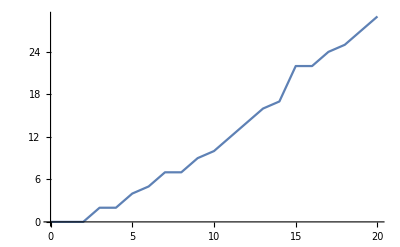

```mathematica
ListPlot[{{0,0},{1,0},{2,0},{3,2},{4,2},{5,4},{6,5},{7,7},{8,7},{9,9},{10,10},{11,12},{12,14},{13,16},{14,17},{15,22},{16,22},{17,24},{18,25},{19,27},{20,29}},Joined->True]
```

```mathematica
FindInstance[Gamma[n+1]==m^2+1&&1000>{n}>0&&m>0,{m,n},Integers,4]
```

{{m→1,n→2}}